## Tidal Love Numbers of a Slowly-Rotating Neutron Star References: [1] P. Pani , L. Gualtieri, V. Ferrari; “Tidal deformations of a slowly-spinning neutron start” (2015) [2] P. Pani, L. Gualtieri, A. Maselli, V. Ferrari; “Tidal deformations of a spinning compact object”, (2015) --- Review: [3] Paolo Pani, “Advanced methods in Black-Hole Perturbation Theory” (2013)

```mathematica
Quit[];
```

```mathematica
Put[10!,LocalObject["TidalLoveSlowRot_NS.nb"]]
```

LocalObject[file:///home/user/.Wolfram/Objects/TidalLoveSlowRot_NS.nb]

In the original notebook, the command Get was written to “get” whatever file is inside the square brackets.

Here, I changed all Get commands into Import commands, to “import” the necessary files. As a result, one MUST write down the appropriate string of where these files are.

```mathematica
(*Insert /home/user/Downloads/arXiv-1509.02171v3/anc/ (i.e. the appropriate string) for all Get -> Import commands*)
```

Import::argt: Import called with 0 arguments; 1 or 2 arguments are expected.

Import[]

#### Collect equations

```mathematica
$Assumptions={L>1};
```

```mathematica
background=Import["/home/user/Downloads/arXiv-1509.02171v3/anc/background.m"];
ruleP=Union[Import["/home/user/Downloads/arXiv-1509.02171v3/anc/final_eqs_polar-led.m"],{m->0}];
ruleA=Import["/home/user/Downloads/arXiv-1509.02171v3/anc/final_eqs_axial-led.m"];
ruleAL2=Import["/home/user/Downloads/arXiv-1509.02171v3/anc/final_eqs_axial-led_L2.m"];
```

```mathematica
eqB1=M'[r]-(M'[r]/.background)//Simplify;
eqB2=ν'[r]-(ν'[r]/.background)//Simplify;
eqB3=P'[r]-(P'[r]/.background)//Simplify;
eqB4=ω1''[r]-(ω1''[r]/.background)//Simplify;
```

```mathematica
eqP1=H000[L]''[r]-(H000[L]''[r]//.ruleP)//Simplify;
eqP2=h001[-1+L]''[r]-(h001[-1+L]''[r]//.ruleP)//Simplify;
eqP3=h001[1+L]''[r]-(h001[1+L]''[r]//.ruleP)//Simplify;
```

```mathematica
eqP2h=Simplify[eqP2/.H000[L]->Function[r,0]/.h001[-1+L]->Function[r,yAm1h[r]]];
eqP3h=Simplify[eqP3/.H000[L]->Function[r,0]/.h001[1+L]->Function[r,yAp1h[r]]];
```

```mathematica
eqA1=h000[L]''[r]-(h000[L]''[r]//.ruleA)//Simplify;
eqA2=H001[-1+L]''[r]-(H001[-1+L]''[r]//.ruleA)//Simplify;
eqA3=H001[1+L]''[r]-(H001[1+L]''[r]//.ruleA)//Simplify;
```

```mathematica
eqA2h=Simplify[eqA2/.h000[L]->Function[r,0]/.H001[-1+L]->Function[r,yPm1h[r]]];
eqA3h=Simplify[eqA3/.h000[L]->Function[r,0]/.H001[1+L]->Function[r,yPp1h[r]]];
```

```mathematica
eqAL22=H001[1]'[r]-(H001[1]'[r]//.ruleAL2)//Simplify;
eqAL23a=H001[3]''[r]-(H001[3]''[r]//.ruleAL2)//Simplify;
eqAL23b=K01[3]'[r]-(K01[3]'[r]//.ruleAL2)//Simplify;
```

```mathematica
eqAL23ah=Simplify[eqAL23a/.h000[2]->Function[r,0]/.H001[3]->Function[r,y2h[r]]];
```

```mathematica
rule={H000[L]->Function[r,yP0[r]],h001[-1+L]->Function[r,yAm1[r]],h001[1+L]->Function[r,yAp1[r]],h000[L]->Function[r,yA0[r]],H001[-1+L]->Function[r,yPm1[r]],H001[1+L]->Function[r,yPp1[r]],
H001[1]->Function[r,y1[r]],H001[3]->Function[r,y2[r]],K01[3]->Function[r,y3[r]],h000[2]->Function[r,yA0[r]]};
```

```mathematica
eqψ=ψ''[r]+(1/(r^2(1-2M[r]/r)))(2M[r]+κ(P[r]-ρ[r])r^3)ψ'[r]-(1/(1-2M[r]/r))((L(L+1))/r^2-6 M[r]/r^3+κ(ρ[r]-P[r]))ψ[r];(*equation in Damour & Nagar*)
```

```mathematica
EQS={eqB1,eqB2,eqB3,eqB4,eqP1,eqP2,eqP3,eqA1,eqA2,eqA3,eqAL22,0eqAL23a,eqP2h,eqP3h,eqA2h,eqA3h,0eqAL23ah,eqψ}/.rule;
Put[EQS,"/home/user/Downloads/arXiv-1509.02171v3/anc/final_system.m"];
```

### Exterior analytical solution

NOTE: this can be generalized to any integer L
Notation: γ2 = γ_2 and γs2 = γ_2^* in the notation of [1].

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
$Assumptions={r>2mass>0,y>2};
```

```mathematica
EQS=Import["/home/user/Downloads/arXiv-1509.02171v3/anc/final_system.m"];
```

#### l=2

```mathematica
ruleEXT={L->2,ρ->Function[r,0],P->Function[r,0],M->Function[r,mass],ν->Function[r,Log[1-(2 mass)/r]],ω1->Function[r,Ω-(2 J)/r^3],yP0->Function[r,-(2 r^2 (-2 mass+r)^2 α2+2 mass (mass-r) (2 mass^2+6 mass r-3 r^2) γ2+3 r^2 (-2 mass+r)^2 γ2 Log[1-(2 mass)/r])/(2 mass^2 (2 mass-r) r)],yAm1->Function[r,1/(30 mass^3 r^2)(30 J mass^3 r γ21+√15 J (2 mass (-2 mass^3 γ2+5 r^2 (2 r α2+3 mass γ2-3 r γ2))-3 r (4 mass^3-10 mass r^2+5 r^3) γ2 Log[1-(2 mass)/r]))],yAp1->Function[r,1/(6720 mass^5 r^2)J (8 √35 (16 mass^4 r (-4 mass+5 r) α2+3 mass (16 mass^5+44 mass^4 r-90 mass^3 r^2-270 mass^2 r^3+945 mass r^4-405 r^5) γ2-3 r (64 mass^5-80 mass^4 r+1080 mass^2 r^3-1350 mass r^4+405 r^5) γ2 ArcTanh[mass/(mass-r)])+105 r γ23 (-2 mass (4 mass^4+10 mass^3 r+30 mass^2 r^2-105 mass r^3+45 r^4)-15 r^3 (-2 mass+r) (-4 mass+3 r) Log[1-(2 mass)/r]))],yA0->Function[r,1/(24 mass^2 r)(24 r^4 αs2+4 mass^4 γs2+4 mass^3 r γs2+6 mass^2 r^2 γs2-6 mass r^3 (8 αs2+γs2)+3 (2 mass-r) r^3 γs2 Log[1-(2 mass)/r])],y1->Function[r,1/(120 mass^4 r^3 (-2 mass+r)^2)(120 J mass^4 r^3 γs21+√15 J mass (-24 (9 mass-10 r) r^3 (-2 mass+r)^2 αs2+2 mass (-8 mass^5+2 mass^4 r+16 mass^3 r^2+117 mass r^4-30 r^5) γs2+3 (9 mass-10 r) r^3 (-2 mass+r)^2 γs2 Log[1-(2 mass)/r]))],yPp1->Function[r,1/(140 mass^5 (2 mass-r) r^4)(2 mass (√35 J (36 mass^2 r^4 (-2 mass+r) αs2+(-4 mass^7-2 mass^6 r+6 mass^5 r^2+23 mass^4 r^3+61 mass^3 r^4-455 mass^2 r^5+420 mass r^6-105 r^7) γs2)+70 J mass^2 r^3 (2 mass^4+10 mass^3 r-65 mass^2 r^2+60 mass r^3-15 r^4) γs23/mass^2)+3 (2 mass-r) r^4 (√35 J (3 mass^3+70 mass^2 r-105 mass r^2+35 r^3) γs2+350 J mass^2 r (2 mass^2-3 mass r+r^2) γs23/mass^2) Log[1-(2 mass)/r])],ψ->Function[r,(BP r^3)/mass^3-(5 BQ (mass (6 mass^3+4 mass^2 r+3 mass r^2+3 r^3)+3 r^4 ArcTanh[mass/(mass-r)]))/(48 mass^3 r)]};
FullSimplify[Join[Take[EQS,{1,8}],Take[EQS,{10,11}],{EQS[[18]]}]//.ruleEXT,r>2mass>0]
```

{0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Put[ruleEXT/.J->JJ,"/home/user/Downloads/arXiv-1509.02171v3/anc/ruleEXT_L2.m"];
```

#### l=3

```mathematica
ruleEXT={L->3,ρ->Function[r,0],P->Function[r,0],M->Function[r,mass],ν->Function[r,Log[1-(2 mass)/r]],ω1->Function[r,Ω-(2 J)/r^3],yP0->Function[r,1/(2 mass^3 (2 mass-r) r)(2 (mass-r) r^2 (-2 mass+r)^2 α3+2 mass (2 mass^4+10 mass^3 r-65 mass^2 r^2+60 mass r^3-15 r^4) γ3+15 (mass-r) r^2 (-2 mass+r)^2 γ3 Log[1-(2 mass)/r])],yAm1->Function[r,1/(4200 mass^4 r^2)J (4 √35 mass (15 r^4 (14 α3-177 γ3)+40 mass^2 r^2 (2 α3-57 γ3)+mass^3 r (32 α3-30 γ3)+60 mass^4 γ3+15 mass r^3 (-32 α3+387 γ3))+350 mass r (2 mass^3+2 mass^2 r+3 mass r^2-3 r^3) γ32+15 r (2 √35 (32 mass^4+80 mass^3 r-480 mass^2 r^2+564 mass r^3-177 r^4) γ3+35 (2 mass-r) r^3 γ32) Log[1-(2 mass)/r])],yAp1->Function[r,1/(3360 mass^6 r^2)J (2 mass (2 √7 (16 mass^3 r (2 mass^2-9 mass r+5 r^2) α3-5 (16 mass^6+76 mass^5 r-762 mass^4 r^2-2610 mass^3 r^3+19865 mass^2 r^4-21315 mass r^5+6090 r^6) γ3)+49 r (4 mass^5+18 mass^4 r+90 mass^3 r^2-685 mass^2 r^3+735 mass r^4-210 r^5) γ34)+15 r (2 √7 (32 mass^6-144 mass^5 r+80 mass^4 r^2+5800 mass^3 r^3-13050 mass^2 r^4+9135 mass r^5-2030 r^6) γ3+49 (2 mass-r) r^3 (20 mass^2-35 mass r+14 r^2) γ34) Log[1-(2 mass)/r])],yA0->Function[r,1/(192 mass^3 r)(64 (4 mass-3 r) (2 mass-r) r^3 αs3-6 mass (4 mass^4+10 mass^3 r+30 mass^2 r^2-105 mass r^3+45 r^4) γs3-45 (4 mass-3 r) (2 mass-r) r^3 γs3 Log[1-(2 mass)/r])],yPm1->Function[r,-1/(2240 mass^4 (2 mass-r) r^4)J (2 √35 (-128 mass (19 mass-6 r) (2 mass-r) r^4 αs3+3 mass (16 mass^6+24 mass^5 r+72 mass^4 r^2+90 mass^3 r^3-3120 mass^2 r^4+4005 mass r^5-1215 r^6) γs3)+2240 mass (mass-r) r^3 (2 mass^2+6 mass r-3 r^2) γs32+15 (2 mass-r) r^4 (3 √35 (76 mass^2-186 mass r+81 r^2) γs3+224 (2 mass-r) r γs32) Log[1-(2 mass)/r])],yPp1->Function[r,1/(2688 mass^6 (2 mass-r) r^4)J (2 √7 (256 mass^3 (9 mass-8 r) (2 mass-r) r^4 αs3+mass (96 mass^8+144 mass^7 r-240 mass^6 r^2-2260 mass^5 r^3-2340 mass^4 r^4+109920 mass^3 r^5-202100 mass^2 r^6+123375 mass r^7-24675 r^8) γs3)-1344 mass (mass-r) r^3 (4 mass^4+40 mass^3 r-440 mass^2 r^2+420 mass r^3-105 r^4) γs34-15 (2 mass-r) r^4 (√7 (216 mass^4+2628 mass^3 r-7990 mass^2 r^2+6580 mass r^3-1645 r^4) γs3+672 (2 mass-r) r (6 mass^2-14 mass r+7 r^2) γs34) Log[1-(2 mass)/r])]};
Simplify[Take[EQS,{1,10}]//.ruleEXT]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
Put[ruleEXT/.J->JJ,"/home/user/Downloads/arXiv-1509.02171v3/anc/ruleEXT_L3.m"];
```

#### l=4

```mathematica
ruleEXT={L->4,ρ->Function[r,0],P->Function[r,0],M->Function[r,mass],ν->Function[r,Log[1-(2 mass)/r]],ω1->Function[r,Ω-(2 J)/r^3],yP0->Function[r,-1/(28 mass^4 (2 mass-r) r)(4 r^2 (-2 mass+r)^2 (6 mass^2-14 mass r+7 r^2) α4+7 (8 mass^6+72 mass^5 r+120 mass^4 (-8) r^2+40 mass^3 43 r^3+150 mass^2 (-7) r^4+210 mass r^5) γ4+105 r^2 (-2 mass+r)^2 (6 mass^2-14 mass r+7 r^2) γ4 Log[1-(2 mass)/r])],yAm1->Function[r,-1/(28224 mass^5 r^2)J (8 √7 mass (7 mass r^4 (512 α4-31185 γ4)+30 mass^3 r^2 (16 α4-1435 γ4)+336 mass^5 γ4+4 mass^4 r (16 α4+35 γ4)+210 mass^2 r^3 (-16 α4+869 γ4)+63 r^5 (-16 α4+1125 γ4))+882 mass r (4 mass^4+10 mass^3 r+30 mass^2 r^2-105 mass r^3+45 r^4) γ43+105 r (4 √7 (32 mass^5+240 mass^4 r-1680 mass^3 r^2+3592 mass^2 r^3-2754 mass r^4+675 r^5) γ4+63 (4 mass-3 r) (2 mass-r) r^3 γ43) Log[1-(2 mass)/r])],yAp1->Function[r,1/(443520 mass^7 r^2)J (16 √11 (-16 mass^4 r (16 mass^3-168 mass^2 r+240 mass r^2-85 r^3) α4+35 mass (48 mass^7+344 mass^6 r-8256 mass^5 r^2-31980 mass^4 r^3+459270 mass^3 r^4-884520 mass^2 r^5+586845 mass r^6-127575 r^7) γ4-105 r (128 mass^7-1344 mass^6 r+1920 mass^5 r^2+112720 mass^4 r^3-396900 mass^3 r^4+476280 mass^2 r^5-238140 mass r^6+42525 r^7) γ4 ArcTanh[mass/(mass-r)])+3465 r γ45 (-2 mass (8 mass^6+56 mass^5 r+420 mass^4 r^2-5670 mass^3 r^3+10920 mass^2 r^4-7245 mass r^5+1575 r^6)-105 (2 mass-r) r^3 (20 mass^3-60 mass^2 r+54 mass r^2-15 r^3) Log[1-(2 mass)/r]))],yA0->Function[r,1/(3360 mass^4 r)(240 r^3 (-40 mass^3+90 mass^2 r-63 mass r^2+14 r^3) αs4+98 mass (4 mass^5+18 mass^4 r+90 mass^3 r^2-685 mass^2 r^3+735 mass r^4-210 r^5) γs4+735 (2 mass-r) r^3 (20 mass^2-35 mass r+14 r^2) γs4 Log[1-(2 mass)/r])],yPm1->Function[r,1/(35280 mass^6 (2 mass-r) r^4)(2 mass (√7 J (-240 mass (2 mass-r) r^4 (365 mass^2-518 mass r+140 r^2) αs4+49 mass (24 mass^7+68 mass^6 r+300 mass^5 r^2+856 mass^4 r^3-36360 mass^3 r^4+102095 mass^2 r^5-80220 mass r^6+19005 r^7) γs4)+17640 J mass r^3 (2 mass^4+10 mass^3 r-65 mass^2 r^2+60 mass r^3-15 r^4) γs43)+735 J mass (2 mass-r) r^4 (√7 (730 mass^3-3570 mass^2 r+4081 mass r^2-1267 r^3) γs4+360 (mass-r) (2 mass-r) r γs43) Log[1-(2 mass)/r])],yPp1->Function[r,1/(55440 mass^7 (2 mass-r) r^4)J (-2 √11 (240 mass^3 (2 mass-r) r^4 (175 mass^2-382 mass r+175 r^2) αs4+49 mass (24 mass^9+68 mass^8 r-60 mass^7 r^2-1562 mass^6 r^3+6882 mass^5 r^4+128834 mass^4 r^5-421890 mass^3 r^6+462735 mass^2 r^7-213570 mass r^8+35595 r^9) γs4)+27720 mass r^3 (4 mass^6+56 mass^5 r-1288 mass^4 r^2+3780 mass^3 r^3-4095 mass^2 r^4+1890 mass r^5-315 r^6) γs45+735 (2 mass-r) r^4 (√11 (350 mass^5+2400 mass^4 r-13888 mass^3 r^2+20566 mass^2 r^3-11865 mass r^4+2373 r^5) γs4+1980 (mass-r) (2 mass-r) r (2 mass^2-6 mass r+3 r^2) γs45) Log[1-(2 mass)/r])]};
FullSimplify[Take[EQS,{1,10}]//.ruleEXT]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
Put[ruleEXT/.J->JJ,"/home/user/Downloads/arXiv-1509.02171v3/anc/ruleEXT_L4.m"];
```

#### Full exterior metric

```mathematica
Quit[];
```

```mathematica
r2=Import["/home/user/Downloads/arXiv-1509.02171v3/anc/ruleEXT_L2.m"]/.JJ->J;
r3=Import["/home/user/Downloads/arXiv-1509.02171v3/anc/ruleEXT_L3.m"]/.JJ->J;
r4=Import["/home/user/Downloads/arXiv-1509.02171v3/anc/ruleEXT_L4.m"]/.JJ->J;
(****)
background={};
ruleP=Union[Import["/home/user/Downloads/arXiv-1509.02171v3/anc/final_eqs_polar-led.m"],{m->0}];
ruleA=Import["/home/user/Downloads/arXiv-1509.02171v3/anc/final_eqs_axial-led.m"];
ruleAL2=Import["/home/user/Downloads/arXiv-1509.02171v3/anc/final_eqs_axial-led_L2.m"];
(*****)
```

```mathematica
X[θ_]:=Sin[θ]^2;
P2[θ_]:=1/2(3(1-X[θ])-1);
Y[θ_,φ_]:=SphericalHarmonicY[l,0,θ,φ];
Sθ[θ_,φ_]:=-1/Sin[θ] D[Y[θ,φ],φ];
Sφ[θ_,φ_]:=Sin[θ]D[Y[θ,φ],θ];
ω[r_]:=Ω-ω1[r];

λ[r_]:=-Log[1-2 M[r]/r];
(*our η is h in HT,ie.η0=h0 etc...,this avoids confusion with the axial perturbations*)

gdd0={{-Exp[ν[r]] (1+ϵa^2 2 (η0[r]+η2[r] P2[θ]))+ϵa^2 ω[r]^2 r^2 X[θ],0,0,-ϵa ω[r] X[θ] r^2},{0,(1-2 M[r]/r)^-1 (1+2 ϵa^2 (m0[r]+m2[r] P2[θ])/(r-2 M[r])),0,0},{0,0,r^2 (1+2 ϵa^2 (v2[r]-η2[r]) P2[θ]),0},{-ϵa ω[r] X[θ] r^2,0,0,r^2 (1+2 ϵa^2 (v2[r]-η2[r]) P2[θ]) X[θ]}};

(*gdd0={{-Exp[ν[r]],0,0,-X[θ]ϵa ω[r]r^2},{0,Exp[λ[r]],0,0},{0,0,r^2,0},{-X[θ]ϵa ω[r]r^2,0,0,r^2X[θ]}};*)
(****)

gddPOLAR=ϵp {{Exp[ν[r]] H0[r] Y[θ,φ],H1[r] Y[θ,φ],0,0},{H1[r] Y[θ,φ],Exp[λ[r]] H2[r] Y[θ,φ],0,0},{0,0,r^2 KK[r] Y[θ,φ],0},{0,0,0,r^2 KK[r] Y[θ,φ] X[θ]}};
gddAXIAL=ϵp {{0,0,h0[r] Sθ[θ,φ],h0[r] Sφ[θ,φ]},{0,0,h1[r] Sθ[θ,φ],h1[r] Sφ[θ,φ]},{h0[r] Sθ[θ,φ],h1[r] Sθ[θ,φ],0,0},{h0[r] Sφ[θ,φ],h1[r] Sφ[θ,φ],0,0}};

ORDERa=1;dim=Length[gdd0];
```

```mathematica
GPL[L0_]:=(
rulePP={H0[r]->H000[l][r],H1[r]->0H100[l][r]+ϵa H101[l][r],H2[r]->H200[l][r],KK[r]->K00[l][r]};
ruleAA={h0[r]->ϵa h001[l][r],h1[r]->ϵa h101[l][r]};
ruleC={H000[L]->Function[r,yP0[r]],h001[L-1]->Function[r,yAm1[r]],h001[L+1]->Function[r,yAp1[r]]};
rL={r2,r3,r4}[[L0-1]];
ruleT=Union[rL,ruleP,rulePP,ruleAA,ruleC,background];
(*****)
gddPOLARL=gddPOLAR//.Union[ruleT,{l->L}];
gddAXIALLp1=gddAXIAL//.Union[ruleT,{l->L+1}];
gddAXIALLm1=gddAXIAL//.Union[ruleT,{l->L-1}];
(*****)
Normal[Series[gddPOLARL+gddAXIALLm1+gddAXIALLp1/.{},{ϵa,0,ORDERa},{ϵp,0,1}]]//Simplify
);
```

```mathematica
GAL[L0_]:=(
(****)
If[L0==2,
{
ruleSOL=ruleAL2;rulePP={H0[r]->ϵa H001[l][r],H1[r]->ϵa H101[l][r],H2[r]->ϵa H201[l][r],KK[r]->0};
ruleC={h000[2]->Function[r,yA0[r]],H001[1]->Function[r,y1[r]],H001[3]->Function[r,yPp1[r]]};
},{
ruleSOL=ruleA;
rulePP={H0[r]->ϵa H001[l][r],H1[r]->ϵa H101[l][r],H2[r]->ϵa H201[l][r],KK[r]->ϵa K01[l][r]};
ruleC={h000[L]->Function[r,yA0[r]],H001[L+1]->Function[r,yPp1[r]],H001[L-1]->Function[r,yPm1[r]]};
}
];
(****)
ruleAA={h0[r]->h000[l][r],h1[r]->h100[l][r]};
rL={r2,r3,r4}[[L0-1]];

ruleT=Union[rL,ruleSOL,rulePP,ruleAA,ruleC,background];
(*****)
gddAXIALL=gddAXIAL//.Union[ruleT,{l->L}];
gddPOLARLp1=gddPOLAR//.Union[ruleT,{l->L+1}];
gddPOLARLm1=gddPOLAR//.Union[ruleT,{l->L-1}];
(*****)
Normal[Series[gddAXIALL+gddPOLARLp1+gddPOLARLm1/.{},{ϵa,0,ORDERa},{ϵp,0,1}]]//Simplify
);
```

```mathematica
gddPv=ParallelTable[GPL[i],{i,2,4}];
```

```mathematica
gddAv=ParallelTable[GAL[i],{i,2,4}];
```

```mathematica
gdd=Normal[Series[(gdd0/.r2)+Sum[gddPv[[i]]+gddAv[[i]],{i,1,3}],{ϵa,0,ORDERa},{ϵp,0,1}]];
```

```mathematica
Put[gdd,"/home/user/Downloads/arXiv-1509.02171v3/anc/full_metric_L234_AP.m"];
```

```mathematica
gdd=Import["/home/user/Downloads/arXiv-1509.02171v3/anc/full_metric_L234_AP.m"];
```

```mathematica
gdd=Normal[Series[Import["/home/user/Downloads/arXiv-1509.02171v3/anc/full_metric_L234_AP.m"]//.{J->Jnew(1+((140 √5 γ2-70 √3 γ21) ϵp)/(280 √π)),mass->M,Jnew->χn M^2},{ϵa,0,ORDERa},{ϵp,0,1}]];
```

```mathematica
Put[gdd,"/home/user/Downloads/arXiv-1509.02171v3/anc/full_metric_L234_AP_rescaled.m"];
```

#### Rotational Love numbers

```mathematica
Quit[];
```

```mathematica
gdd=Import["/home/user/Downloads/arXiv-1509.02171v3/anc/full_metric_L234_AP_rescaled.m"];
```

```mathematica
g00s=Series[gdd[[1]][[1]],{r,∞,6}];
g03s=Series[gdd[[1]][[4]],{r,∞,6}];
```

```mathematica
ss=SeriesCoefficient[g00s,4];
ii0=Integrate[Sin[θ]Conjugate[LegendreP[3,Cos[θ]]]ss,{θ,0,π}];
```

```mathematica
ii0//Expand
```

-(8 M^4 γ3 ϵp)/(7 √(7 π))-(8 M^4 γs23 ϵa ϵp χn)/(7 √(7 π))+(91 M^4 γs4 ϵa ϵp χn)/(45 √π)-(8 M^4 γs43 ϵa ϵp χn)/(7 √(7 π))

```mathematica
ss=SeriesCoefficient[g03s,4];
ii0=Integrate[Sin[θ]Conjugate[D[SphericalHarmonicY[4,0,θ,φ],θ]] ss/Sin[θ],{θ,0,π}]
```

-(10 M^5 ϵp (49 γs4+(374 √7 γ3+49 γ34) ϵa χn))/(441 π)

ELECTRIC

```mathematica
δKE[L_]:=(
ss=SeriesCoefficient[g00s,L+1];
ii0=Integrate[Sin[θ]Conjugate[LegendreP[L,Cos[θ]]]ss,{θ,0,π}];
αv=ϵp{α1,α2,α3,α4,α5};
αsv=ϵp{αs1,αs2,αs3,αs4,αs5};
coeff={1/M^2,(5 √(5 π))/(8 M^3),(7 √(7 π))/(8 M^4),(63 √π)/(32 M^5),1/M^6};
ii=coeff[[L]]ii0;
If[Or[L==1,L==5],
δK0=0;
δK1=(D[ii,ϵa]/.ϵa->0)ϵa
,
δK0=ii/αv[[L]]/.ϵa->0;
δK1=(D[ii,ϵa]/.ϵa->0)ϵa;
];

{δK0,δK1}
);
```

```mathematica
dKe1=δKE[1]
dKe2=δKE[2]
dKe3=δKE[3]
dKe4=δKE[4]
dKe5=δKE[5]
```

{0,((121 √5 γs2+20 √3 γs21) ϵa ϵp χn)/(60 √π)}

{-γ2/α2,-((-375 √7 γs3+224 √5 γs32) ϵa ϵp χn)/(224 √5)}

{-γ3/α3,-((360 √7 γs23-4459 γs4+360 √7 γs43) ϵa ϵp χn)/(360 √7)}

{-γ4/(2 α4),-((-17 √7 γs3+672 γs34) ϵa ϵp χn)/1344}

{0,(4 (199 γs4-180 √11 γs45) ϵa ϵp χn)/(16335 √π)}

```mathematica
δKe12=dKe1[[2]]/(ϵp αs2)
δKe23=dKe2[[2]]/(ϵp αs3);
δKe32=(D[dKe3[[2]],γs2]γs2+D[dKe3[[2]],γs23]γs23)/(ϵp αs2)//Simplify
δKe34=(D[dKe3[[2]],γs4]γs4+D[dKe3[[2]],γs43]γs43)/(ϵp αs4)//Simplify
δKe43=dKe4[[2]]/(ϵp αs3)//Simplify
δKe54=dKe5[[2]]/(ϵp αs4)//Simplify
```

((121 √5 γs2+20 √3 γs21) ϵa χn)/(60 √π αs2)

-(γs23 ϵa χn)/αs2

((637 √7 γs4-360 γs43) ϵa χn)/(360 αs4)

((17 √7 γs3-672 γs34) ϵa χn)/(1344 αs3)

(4 (199 γs4-180 √11 γs45) ϵa χn)/(16335 √π αs4)

MAGNETIC

```mathematica
δKM[L_]:=(
ss=SeriesCoefficient[g03s,L];
ii0=Integrate[Sin[θ]Conjugate[D[SphericalHarmonicY[L,0,θ,φ],θ]] ss/Sin[θ],{θ,0,π}];
αv=ϵp{α1,α2,α3,α4,α5};
αsv=ϵp{αs1,αs2,αs3,αs4,αs5};
coeff={1/M^2,-π/(288 M^3),-π/(2048 M^4),-π/(12800 M^5),1/M^6};
ii=coeff[[L]]ii0;
If[Or[L==1,L==5],
δK0=0;
δK1=(D[ii,ϵa]/.ϵa->0)ϵa
,
δK0=ii/αsv[[L]]/.ϵa->0;
δK1=(D[ii,ϵa]/.ϵa->0)ϵa;
];
{δK0,δK1}
);
```

```mathematica
dKm1=δKM[1]
dKm2=δKM[2]
dKm3=δKM[3]
dKm4=δKM[4]
dKm5=δKM[5]
```

{0,(4 ϵa χn)/(√(3 π))}

{γs2/(480 αs2),((74 √35 γ3+35 γ32) ϵa ϵp χn)/16800}

{(3 γs3)/(7168 αs3),((44 √35 γ2+3 (7 γ23+44 √7 γ4+7 γ43)) ϵa ϵp χn)/50176}

{γs4/(11520 αs4),((374 √7 γ3+49 γ34) ϵa ϵp χn)/564480}

{0,-(3 (2872 √11 γ4+385 γ45) ϵa ϵp χn)/(847 π)}

```mathematica
δKm23=dKm2[[2]]/(ϵp α3);
δKm32=(D[dKm3[[2]],γ2]γ2+D[dKm3[[2]],γ23]γ23)/(ϵp α2)//Simplify;
δKm34=(D[dKm3[[2]],γ4]γ4+D[dKm3[[2]],γ43]γ43)/(ϵp α4)//Simplify;
δKm43=dKm4[[2]]/(ϵp α3)//Simplify;
δKm54=dKm5[[2]]/(ϵp α4)//Simplify;
```

```mathematica
gammastoK=Solve[{dKe2[[1]]==KE2,dKe3[[1]]==KE3,dKe4[[1]]==KE4,δKe12==δKE12,δKe23==δKE23,δKe32==δKE32,δKe34==δKE34,δKe43==δKE43,δKe54==δKE54,dKm2[[1]]==KM2,dKm3[[1]]==KM3,dKm4[[1]]==KM4,δKm23==δKM23,δKm32==δKM32,δKm34==δKM34,δKm43==δKM43,δKm54==δKM54},{KE2,KE3,KE4,δKE12,δKE23,δKE32,δKE34,δKE43,δKE54,KM2,KM3,KM4,δKM23,δKM32,δKM34,δKM43,δKM54}][[1]]//FullSimplify
```

{KE2→-γ2/α2,KE3→-γ3/α3,KE4→-γ4/(2 α4),δKE12→((121 √5 γs2+20 √3 γs21) ϵa χn)/(60 √π αs2),δKE23→((75 √35 γs3-224 γs32) ϵa χn)/(224 αs3),δKE32→-(γs23 ϵa χn)/αs2,δKE34→((637 √7 γs4-360 γs43) ϵa χn)/(360 αs4),δKE43→((17 √7 γs3-672 γs34) ϵa χn)/(1344 αs3),δKE54→(4 (199 γs4-180 √11 γs45) ϵa χn)/(16335 √π αs4),KM2→γs2/(480 αs2),KM3→(3 γs3)/(7168 αs3),KM4→γs4/(11520 αs4),δKM23→((74 √35 γ3+35 γ32) ϵa χn)/(16800 α3),δKM32→((44 √35 γ2+21 γ23) ϵa χn)/(50176 α2),δKM34→(3 (44 √7 γ4+7 γ43) ϵa χn)/(50176 α4),δKM43→((374 √7 γ3+49 γ34) ϵa χn)/(564480 α3),δKM54→-(3 (2872 √11 γ4+385 γ45) ϵa χn)/(847 π α4)}

```mathematica
Put[gammastoK,"/home/user/Downloads/arXiv-1509.02171v3/anc/gammastoK.m"];
```

```mathematica
Ktogammas=Solve[{dKe2[[1]]==KE2,dKe3[[1]]==KE3,dKe4[[1]]==KE4,δKe12==δKE12,δKe23==δKE23,δKe32==δKE32,δKe34==δKE34,δKe43==δKE43,δKe54==δKE54,dKm2[[1]]==KM2,dKm3[[1]]==KM3,dKm4[[1]]==KM4,δKm23==δKM23,δKm32==δKM32,δKm34==δKM34,δKm43==δKM43,δKm54==δKM54},{γ2,γ3,γ4,γs21,γs32,γs23,γs43,γs34,γs45,γs2,γs3,γs4,γ32,γ23,γ43,γ34,γ45}][[1]]//FullSimplify
```

{γ2→-KE2 α2,γ3→-KE3 α3,γ4→-2 KE4 α4,γs21→-968 √15 KM2 αs2+(√(3 π) αs2 δKE12)/(ϵa χn),γs32→800 √35 KM3 αs3-(αs3 δKE23)/(ϵa χn),γs23→-(αs2 δKE32)/(ϵa χn),γs43→20384 √7 KM4 αs4-(αs4 δKE34)/(ϵa χn),γs34→544/9 √7 KM3 αs3-(2 αs3 δKE43)/(ϵa χn),γs45→(12736 KM4 αs4)/(√11)-(33 √(11 π) αs4 δKE54)/(16 ϵa χn),γs2→480 KM2 αs2,γs3→(7168 KM3 αs3)/3,γs4→11520 KM4 αs4,γ32→(74 KE3 α3)/(√35)+(480 α3 δKM23)/(ϵa χn),γ23→44/3 √(5/7) KE2 α2+(7168 α2 δKM32)/(3 ϵa χn),γ43→(88 KE4 α4)/(√7)+(7168 α4 δKM34)/(3 ϵa χn),γ34→(374 KE3 α3)/(7 √7)+(11520 α3 δKM43)/(ϵa χn),γ45→(5744 KE4 α4)/(35 √11)-(11 π α4 δKM54)/(15 ϵa χn)}

The above is what we need!

```mathematica
gddF=Normal[Series[Import["/home/user/Downloads/arXiv-1509.02171v3/anc/full_metric_L234_AP_rescaled.m"]//.Ktogammas,{ϵa,0,ORDERa},{ϵp,0,1}]]//Simplify;
```

```mathematica
Put[gddF,"/home/user/Downloads/arXiv-1509.02171v3/anc/full_metric_L234_AP_final.m"];
```

```mathematica
Put[Ktogammas,"/home/user/Downloads/arXiv-1509.02171v3/anc/Ktogammas.m"];
```

```mathematica
gdd=Import["/home/user/Downloads/arXiv-1509.02171v3/anc/full_metric_L234_AP_final.m"];
```

```mathematica
Series[gdd[[1]][[4]]/.{α4->0,α3->0,αs2->0,αs3->0,αs4->0},{r,∞,5}]//Simplify
```

-√(5/π) α2 ϵa ϵp χn Sin[θ]^2 r-1/4 M √(5/π) α2 ϵa ϵp χn (3+5 Cos[2 θ]) Sin[θ]^2+(M^2 ϵa χn (-10 √π+3 √5 α2 ϵp+5 √5 α2 ϵp Cos[2 θ]) Sin[θ]^2)/(5 √π r)+(128 M^4 √(7/π) α2 δKM32 ϵp (3+5 Cos[2 θ]) Sin[θ]^2)/r^3+(M^5 α2 ϵp (3200 √7 δKM32+3 √5 KE2 ϵa χn) (3+5 Cos[2 θ]) Sin[θ]^2)/(10 √π r^4)+(4 M^6 α2 ϵp (16800 √7 δKM32+22 √5 KE2 ϵa χn+35 (800 √7 δKM32+√5 KE2 ϵa χn) Cos[2 θ]) Sin[θ]^2)/(35 √π r^5)+O[1/r]^6

At this point, we stop here. Finding these Gamma values was the motivation behind these import file changes.

The rest of the notebook remains unchanged; if one is interested to follow the last part through, make the necessary Get -> Import edits.

#### RULES (to extract the integration constants from the values of the functions at the radius)

```mathematica
Quit[];
```

```mathematica
r2=Get["ruleEXT_L2.m"];
r3=Get["ruleEXT_L3.m"];
r4=Get["ruleEXT_L4.m"];
```

```mathematica
(*BP and BQ are computed only for L=2*)
```

```mathematica
ruleLOVE0=Solve[Union[{yP0[r]==Y1,yP0'[r]==Y1p,yA0[r]==Z1,yA0'[r]==Z1p,ψ[r]==ψR,ψ'[r]==ψpR}//.r2,{yP0[r]==Y1,yP0'[r]==Y1p,yA0[r]==Z1,yA0'[r]==Z1p}//.r3,{yP0[r]==Y1,yP0'[r]==Y1p,yA0[r]==Z1,yA0'[r]==Z1p}//.r4],{α2,γ2,αs2,γs2,α3,γ3,αs3,γs3,α4,γ4,αs4,γs4,BP,BQ}][[1]]//Simplify;
```

```mathematica
ruleLOVE2=Solve[{yAm1[r]==YAm1+CAm1 YAm1h,yAm1'[r]==YAm1p+CAm1 YAm1hp,yAp1[r]==YAp1+CAp1 YAp1h,yAp1'[r]==YAp1p+CAp1 YAp1hp,yPp1[r]==YPp1+CPp1 YPp1h,yPp1'[r]==YPp1p+CPp1 YPp1hp,y1[r]==YY1}//.r2,{CAm1,γ21,CAp1,γ23,CPp1,γs23,γs21}][[1]]//Simplify;
```

```mathematica
ruleLOVE3=Solve[{yAm1[r]==YAm1+CAm1 YAm1h,yAm1'[r]==YAm1p+CAm1 YAm1hp,yAp1[r]==YAp1+CAp1 YAp1h,yAp1'[r]==YAp1p+CAp1 YAp1hp,yPm1[r]==YPm1+CPm1 YPm1h,yPm1'[r]==YPm1p+CPm1 YPm1hp,yPp1[r]==YPp1+CPp1 YPp1h,yPp1'[r]==YPp1p+CPp1 YPp1hp}//.r3,{CAm1,γ32,CAp1,γ34,CPm1,γs32,CPp1,γs34}][[1]]//Simplify;
```

```mathematica
ruleLOVE4=Solve[{yAm1[r]==YAm1+CAm1 YAm1h,yAm1'[r]==YAm1p+CAm1 YAm1hp,yAp1[r]==YAp1+CAp1 YAp1h,yAp1'[r]==YAp1p+CAp1 YAp1hp,yPm1[r]==YPm1+CPm1 YPm1h,yPm1'[r]==YPm1p+CPm1 YPm1hp,yPp1[r]==YPp1+CPp1 YPp1h,yPp1'[r]==YPp1p+CPp1 YPp1hp}//.r4,{CAm1,γ43,CAp1,γ45,CPm1,γs43,CPp1,γs45}][[1]]//Simplify;
```

```mathematica
Put[ruleLOVE0,"ruleLOVE0.m"];
Put[ruleLOVE2,"ruleLOVE2.m"];
Put[ruleLOVE3,"ruleLOVE3.m"];
Put[ruleLOVE4,"ruleLOVE4.m"];
```

### INTEGRATOR

```mathematica
Quit[];
```

```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["GUIKit`"];
```

#### EOS

Here we import the EOS data files [available upon request]. One can clearly use its own dataset. The format required is as follows:
- line #1: number of tabulated points in file
- remaining lines: five columns:

column #1: energy density/c^2 	(g/cm^3)
column #2: pressure		(dynes/cm^2)
column #3: enthalpy 		(cm^2/s^2)
column #4: baryon number density (cm^{-3})
column #5: adiabatic index

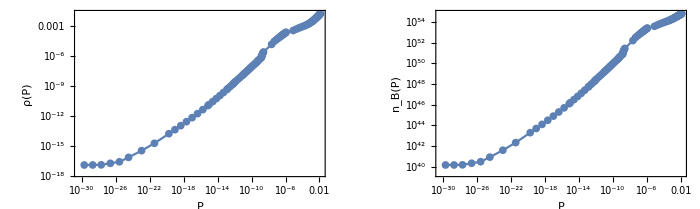

POLY n=1

{0.0127443,0.015811}

1/(1000 √5)

2.31499×10^54

```mathematica
(************)
POLYTROPIC=1;rulePOLY={const->50,n->1};(*=1 for polytropic, =0 otherwise*)
(************)
kg=1/(1.98892 10^30);(*Solar mass units*)
second=1/(4.92549232189886339689643862 10^-6);(*Solar mass units*)
meter=1/(2.99792458 10^8)second;
cm=10^-2 meter;
dyne=(10^-3 kg)/second^2 cm;
cx= (10^-3 kg)/cm^3;
cy=dyne/cm^2;
mb=1.66 10^-27 kg;

cz=cm^-3;
gcm3=1.6188*10^-18;(*g/cm^3 in Msun=1 units*)
km=0.67722;(*km in Msun=1 units*)
(**************)
$Assumptions={η[r]≥0,η0≥0,r≥0};
SetDirectory["/home/paolo/mathematica/EOS/EOS/"];
fileEOS={"poly_Damour","APR_Lorene","eosAPR","eosFPS","eosAPRb","eosA","eospoly","eosMS1","eosMPA1","eosAP4","eosENG","SLy","SLy4.dat","BPAL12.dat","BSK20.dat"};

fileEOS=fileEOS[[8]];
(***)
EOSv=Import[fileEOS,"Table"];

INTORD=1;
(**************third point just to be safe *********************)
EOS=Join[Table[{EOSv[[i]][[2]] cy,EOSv[[i]][[1]]cx},{i,3,Length[EOSv]}]];
EOSinv=Join[Table[{EOSv[[i]][[1]]cx,EOSv[[i]][[2]] cy},{i,3,Length[EOSv]}]];
BN=Table[{EOSv[[i]][[2]] cy,EOSv[[i]][[4]] cz},{i,3,Length[EOSv]}];
(***********************************)
If[POLYTROPIC==0,
rhoP[x_]:=Interpolation[EOS,x,InterpolationOrder->INTORD];
Pρ[x_]:=Interpolation[EOSinv,x,InterpolationOrder->INTORD];
,
rhoP[x_]:=(x/const)^(n/(n+1))//.rulePOLY;
Pρ[x_]:=const x^(1+1/n)//.rulePOLY;
];

barnum[x_]:=Interpolation[BN,x,InterpolationOrder->INTORD];
(***********************************)
ρPT=Table[{EOS[[i]][[1]],rhoP[EOS[[i]][[1]]]},{i,1,Length[EOS]}];
prho=ListLogLogPlot[{EOS},Joined->True,Frame->True,PlotRange->All,Mesh->Automatic,FrameLabel->{"P","ρ(P)"}];
pbn=ListLogLogPlot[BN,Joined->True,Frame->True,PlotRange->All,Mesh->Automatic,FrameLabel->{"P","n_B(P)"}];
GraphicsGrid[{{prho,pbn}},ImageSize->700]
x0=EOSv[[2]][[2]]cy;
(*rhoP[x_]:=Piecewise[{{Interpolation[EOS,x,InterpolationOrder->5],x>x0},{0,x<x0}}];*)

If[POLYTROPIC==0,EOSin={ρ[r]->rhoP[HeavisideTheta[P[r]]P[r]]},EOSin={ρ[r]->(P[r]/const)^(n/(n+1))//.rulePOLY}];
(********************)
If[POLYTROPIC==0,Print[fileEOS],Print["POLY n=",n//.rulePOLY]];
EOS[[Length[EOS]]]
rhoP[10^-5]
barnum[1.5 10^-3]
```

#### Integrator

```mathematica
SetDirectory[NotebookDirectory[]];

INT[Pc0_,L0_,νc0_,ω1c0_,alphaE_,alphaM_,Rs0_,EPS_,AG_,PG_,BINDING_]:=(
ruleP={AccuracyGoal->AG,PrecisionGoal->PG,MaxSteps->5 10^5,MaxStepSize->Automatic};
rc=EPS;
L00=L0;
Pc00=Pc0;
(***************************************)
param={κ->4π,L->L0,Pc[0]->Pc0,νc[0]->νc0,ω1c[0]->ω1c0,yP0c[0]->alphaE,yA0c[0]->alphaM,ψc[0]->1,ρP[x_]->rhoP[x],ρP'[x_]->rhoP'[x],CC->Function[r,1/(√rhoP'[P[r]])]};
(***************************************)
(* Series at the center to construct the BCs*)
RULEc=Get["rulec.m"];
Mg=Sum[Mc[i] r^i,{i,3,5}];
νg=Sum[νc[i] r^i,{i,0,4}];
Pg=Sum[Pc[i] r^i,{i,0,4}];
ω1g=Sum[ω1c[i] r^i,{i,0,4}];
(*****)
yP0g=r^L Sum[yP0c[i] r^i,{i,0,3}];
yA0g=r^(L+1)Sum[yA0c[i] r^i,{i,0,4}];
ψg=r^(L+1)Sum[ψc[i] r^i,{i,0,4}];
(***************************************)
(* Boundary conditions at r=0 for the integration*)
BCs={M[rc]==Mg,ν[rc]==νg,P[rc]==Pg,ω1[rc]==ω1g,ω1'[rc]==D[ω1g,r],yP0[rc]==yP0g,yP0'[rc]==D[yP0g,r],yA0[rc]==yA0g,yA0'[rc]==D[yA0g,r],ψ[rc]==ψg,ψ'[rc]==D[ψg,r]}//.Union[RULEc,param,{r->rc}];
(******)
EQS=Get["final_system.m"];
(** Full system of equations, including the associate homogeneous system and the equations for the tidal deformations**)
EQs=Join[Table[EQS[[i]]==0,{i,1,5}],{EQS[[8]]==0,EQS[[18]]==0}]//.Union[param,EOSin,D[EOSin,r],{(*dPdρ->1/ρP'[P[r]]*)}];
(*List of dynamical variables*)
variables={M,ν,P,ω1,yP0,yA0,ψ};
(**************************)
(***** INTEGRATION FROM THE CENTER TO THE RADIUS *****)
(**************************)
(*Print["before"];*)
solA=NDSolve[Union[EQs,BCs],variables,{r,rc,Rs0},ruleP,Method->{"EventLocator","Event"->P[r]==1 10^-10 Pc0(*Pρ[ 5 10^9 gcm3]*)}(*,Method->"ExplicitRungeKutta"*)]//Chop;
(*Print["after"];*)
Mni=M[r]/.solA[[1]];νni=ν[r]/.solA[[1]];Pni=P[r]/.solA[[1]];
ω1ni=ω1[r]/.solA[[1]];
ρni=rhoP[Pni];
yP0ni=yP0[r]/.solA[[1]];
yA0ni=yA0[r]/.solA[[1]];
ψni=ψ[r]/.solA[[1]];
(********************)
R=InterpolatingFunctionDomain[First[M/.solA]][[1,-1]];
If[Abs[R/Rs0-1]<10^-8,Print["WARNING!!!! NO RADIUS!!!!!"]];
(****)
(* Let's start extracting some physical quantity. We use the analytical exterior solution*)
(***********************************)
MASS=Mni/.r->R;
(***********************************)
Ωs=√(MASS/R^3);
(*ω1inf=Ω-(2 JJ)/r^3;*)
ω1n=ω1ni;
(**************)
(* RESCALING *)
(**************)
omrescal=ω1n+(R D[ω1n,r])/3/.r->R;
g00rescal=Exp[-νni](1-2 MASS/r)/.r->R;
rescal=g00rescal omrescal^2;
(*****)
ω1nibefore=ω1ni;
ω1nbefore=ω1n;
ω1ni=ω1ni Ωs;ω1n=ω1n Ωs;
ω1n=ω1n/omrescal;
(*********************)
(* END OF RESCALING *)
(*********************)
If[BINDING==1,AA=mb NIntegrate[barnum[Pni/.r->x]^1(1-2(Mni/.r->x)/x)^(-1/2)4 π x^2,{x,rc,R}(*,MaxRecursion->20*)],AA=MASS;];
EB=AA-MASS;

(* Let's extract the spin and the angular velocity *)
(*systOmegaJ=NSolve[{ω1n==ω1inf,D[ω1n,r]==D[ω1inf,r]}/.{r->R},{Ω,JJ}][[1]];*)
J=(R^4 D[ω1n,r])/6/.r->R;
Omega=ω1n+(R D[ω1n,r])/3/.r->R;
Inertia=J/Omega;
Rg=√(J/(Omega MASS));
(*******)
(*****)
(*******)
χ=J/MASS^2;
Ibar=Inertia/MASS^3;
(*******)
rule0={mass->MASS,Y1->yP0ni,Y1p->D[yP0ni,r],Z1->yA0ni,Z1p->D[yA0ni,r],ψR->ψni,ψpR->D[ψni,r]}/.r->R;
gammastoK=Get["gammastoK.m"];
ruleLOVE00=Get["ruleLOVE0.m"];
ruleLOVE0=Union[ruleLOVE00,rule0,gammastoK];

λEbar={KE2,KE3,KE4}[[L0-1]]//.ruleLOVE0/.r->R;(*Definitions taken from Yagi Multipole Love [for σ we use Kmag of Poisson]*)
λMbar={KM2,KM3,KM4}[[L0-1]]//.ruleLOVE0/.r->R;
λKENT={BQ/(48BP),BQ/(48BP),BQ/(48BP)}[[L0-1]]//.ruleLOVE0/.r->R;(*the prefactor is irrelevant for the purpose of comparison*)
(*λKENT is valid only for L=2, we didn't compute BQ and BP for other L's*)
(********************************)

{Pc0,rhoP[Pc0],MASS,R,Omega,J,χ,EB,Inertia,Ibar,λEbar,λMbar,λKENT}
);
Print["Done"];
```

Done

```mathematica
density=1 10^15 gcm3;
νini=1;
ωini=1;
INT[Pρ[density],2,νini,ωini,1,1,50,1 10^-4,80,11,0];
Timing[INT[Pρ[density],2,νini+Log[g00rescal],ωini/omrescal,1,1,50,1 10^-4,80,11,0]]
{g00rescal,omrescal,rescal,MASS/R,4/5 λEbar (MASS/R)^5,yA0ni/.r->R,J/MASS^2}
```

{0.05476,{0.000131026,0.0016188,0.880783,7.56029,0.0451468,0.691486,0.891344,0.,15.3164,22.4155,6226.06,4.16114,-16.0585}}

{1.,1.,1.,0.116501,0.106895,664.24,0.891344}

```mathematica
INT3[Pc0_,L0_,νc0_,ω1c0_,alphaE_,alphaM_,Rs0_,EPS_,AG_,PG_,BINDING_]:=(
(***************************************)
norm=1;
ruleP={AccuracyGoal->AG,PrecisionGoal->PG,MaxSteps->5 10^5,MaxStepSize->Automatic};
param2=Union[{Ω->Omega,yAm1c[0]->norm,yAp1c[0]->norm,yPm1c[0]->norm,yPp1c[0]->norm,y1c[1]->norm,(*y2c[3]->1,*)yAm1hc[0]->norm,yAp1hc[0]->norm,yPm1hc[0]->norm,yPp1hc[0]->norm(*,y2hc[3]->1*)}];
(***************************************)
(* Series at the center to construct the BCs*)
Mg=Sum[Mc[i] r^i,{i,3,5}];
νg=Sum[νc[i] r^i,{i,0,4}];
Pg=Sum[Pc[i] r^i,{i,0,4}];
ω1g=Sum[ω1c[i] r^i,{i,0,4}];
(*****)
yP0g=r^L Sum[yP0c[i] r^i,{i,0,3}];
yA0g=r^(L+1)Sum[yA0c[i] r^i,{i,0,4}];
(******)
yAm1g=r^L Sum[yAm1c[i] r^i,{i,0,3}];
yAp1g=r^(L+2)Sum[yAp1c[i] r^i,{i,0,3}];
yPm1g=r^(L-1)Sum[yPm1c[i] r^i,{i,0,2}];
yPp1g=r^(L+1)Sum[yPp1c[i] r^i,{i,0,2}];
y1g=Sum[y1c[i] r^i,{i,0,3}];
(*y2g=Sum[y2c[i] r^i,{i,0,6}];*)
yAm1hg=r^L Sum[yAm1hc[i] r^i,{i,0,3}];
yAp1hg=r^(L+2)Sum[yAp1hc[i] r^i,{i,0,3}];
yPm1hg=r^(L-1)Sum[yPm1hc[i] r^i,{i,0,2}];
yPp1hg=r^(L+1)Sum[yPp1hc[i] r^i,{i,0,2}];
(*y1hg=Sum[y1hc[i] r^i,{i,0,3}];*)
(*y2hg=Sum[y2hc[i] r^i,{i,0,6}];*)

(* Boundary conditions at r=0 for the integration*)
BCs0={M[rc]==Mg,ν[rc]==νg,P[rc]==Pg,ω1[rc]==ω1g,ω1'[rc]==D[ω1g,r],yP0[rc]==yP0g,yP0'[rc]==D[yP0g,r],yA0[rc]==yA0g,yA0'[rc]==D[yA0g,r]}//.Union[RULEc,param,{r->rc}];
BCsL={yAm1[rc]==yAm1g,yAm1'[rc]==D[yAm1g,r],yAp1[rc]==yAp1g,yAp1'[rc]==D[yAp1g,r],yPm1[rc]==yPm1g,yPm1'[rc]==D[yPm1g,r],yPp1[rc]==yPp1g,yPp1'[rc]==D[yPp1g,r],yAm1h[rc]==yAm1hg,yAm1h'[rc]==D[yAm1hg,r],yAp1h[rc]==yAp1hg,yAp1h'[rc]==D[yAp1hg,r],yPm1h[rc]==yPm1hg,yPm1h'[rc]==D[yPm1hg,r],yPp1h[rc]==yPp1hg,yPp1h'[rc]==D[yPp1hg,r]};
BCs2={yAm1[rc]==yAm1g,yAm1'[rc]==D[yAm1g,r],yAp1[rc]==yAp1g,yAp1'[rc]==D[yAp1g,r],y1[rc]==y1g,(*y2[rc]==y2g,y2'[rc]==D[y2g,r],*)yPp1[rc]==yPp1g,yPp1'[rc]==D[yPp1g,r],yAm1h[rc]==yAm1hg,yAm1h'[rc]==D[yAm1hg,r],yAp1h[rc]==yAp1hg,yAp1h'[rc]==D[yAp1hg,r],(*y2h[rc]==y2hg,y2h'[rc]==D[y2hg,r]*)yPp1h[rc]==yPp1hg,yPp1h'[rc]==D[yPp1hg,r]};
If[L00==2,BCs=BCs2,BCs=BCsL];
BCs=Join[BCs,BCs0]//.Union[RULEc,param,param2,{r->rc}];
(******)
(** Full system of equations, including the associate homogeneous system and the equations for the tidal deformations**)
EQs0=Join[Table[EQS[[i]]==0,{i,1,5}],{EQS[[8]]==0}];
EQs2=Join[Table[EQS[[i]]==0,{i,6,7}],Table[EQS[[i]]==0,{i,10,11}],Table[EQS[[i]]==0,{i,13,14}],Table[EQS[[i]]==0,{i,16,16}]];
EQsL=Join[Table[EQS[[i]]==0,{i,6,7}],Table[EQS[[i]]==0,{i,9,10}],Table[EQS[[i]]==0,{i,13,16}]];
If[L00==2,EQs=EQs2,EQs=EQsL];
EQs=Join[EQs,EQs0]//.Union[param,param2,EOSin,D[EOSin,r],{(*dPdρ->1/ρP'[P[r]]*)}];
(****)
(*List of dynamical variables*)
If[L00==2,
variables={M,ν,P,ω1,yP0,yA0,yAm1,yAp1,y1,yPp1,yAm1h,yAp1h,yPp1h},variables={M,ν,P,ω1,yP0,yA0,yAm1,yAp1,yPm1,yPp1,yAm1h,yAp1h,yPm1h,yPp1h}
];
(**************************)
(***** INTEGRATION FROM THE CENTER TO THE RADIUS *****)
(**************************)
(*Print["before"];*)
sol2=NDSolve[Union[EQs,BCs],variables,{r,rc,R},ruleP][[1]];
(*Print["after"];*)
grule={Get["ruleLOVE2.m"],Get["ruleLOVE3.m"],Get["ruleLOVE4.m"]}[[L00-1]];
rulen0={mass->MASS,JJ->J,Y1->yP0ni,Y1p->D[yP0ni,r],Z1->yA0ni,Z1p->D[yA0ni,r]}/.r->R;
(***)
rulen={YAm1->yAm1[r],YAm1h->yAm1h[r],YAm1p->yAm1'[r],YAm1hp->yAm1h'[r],YAp1->yAp1[r],YAp1h->yAp1h[r],YAp1p->yAp1'[r],YAp1hp->yAp1h'[r],(*Y2->y2[r],Y2h->y2h[r],Y2p->y2'[r],Y2hp->y2h'[r],*)YY1->y1[r],YPm1->yPm1[r],YPm1h->yPm1h[r],YPm1p->yPm1'[r],YPm1hp->yPm1h'[r],YPp1->yPp1[r],YPp1h->yPp1h[r],YPp1p->yPp1'[r],YPp1hp->yPp1h'[r]}/.sol2/.r->R;
(***)
ruleLOVE=Union[ruleLOVE0,grule,rulen0,rulen];
(********************************)
v2=1/(χ ϵa χn){δKE12,δKE32,0,δKM32};
v3=1/(χ ϵa χn){δKE23,δKE43,δKM23,δKM43};
v4=1/(χ ϵa χn){δKE34,δKE54,δKM34,δKM54};
love={v2,v3,v4}[[L00-1]]//.ruleLOVE/.sol2/.r->R;
(********************************)
Flatten[{Pc00,rhoP[Pc00],MASS,R,Omega,J,χ,EB,Inertia,Ibar,λEbar,λMbar,λKENT,love}]
);
Print["Done 3"];
```

Done 3

```mathematica
count=0;
νini=1;
ωini=1;
TOT[Pc0_,L0_,ALPHAE_,ALPHAM_,Rs0_,EPS_,AG_,PG_,AG2_,PG2_,BINDING_]:=
(
INT[Pc0,L0,νini,ωini,ALPHAE,ALPHAM,Rs0,EPS,AG,PG,BINDING];
INT[Pc0,L0,νini+Log[g00rescal],ωini/omrescal,ALPHAE,ALPHAM,Rs0,EPS,AG,PG,BINDING];
(*INT2[AG2,PG2]*)
(*Print[{Ibar,λEbar,λMbar}];*)
count++;
INT3[Pc0,L0,1+Log[g00rescal],1/omrescal,ALPHAE,ALPHAM,Rs0,EPS,AG2,PG2,BINDING]
);
```

```mathematica
tt=Timing[TOT[Pρ[0.4 10^15 gcm3],2,1,1,50,1 10^-4,80,11,80,11,0]]
{MASS/R,λEbar(MASS/R)^7,love[[1]](MASS/R)^5,love}
```

{4.06839,{0.0000209641,0.00064752,0.463954,8.26365,0.0286734,0.254439,1.18205,0.,8.87371,88.8548,391302.,103.115,-323.732,-299195.,5.22465×10^6,0.,-10567.8}}

{0.0561439,0.000688067,-0.166904,{-299195.,5.22465×10^6,0.,-10567.8}}

#### Reproducing Table II in [1]

Note that the rotational Love numbers as defined in [1] differ from those returned by the integrator by some numerical coefficient. Here we introduce the normalization factors in order to reproduce Table II in [1]

```mathematica
(* APS: C=(0.1,0.15,0.2)=(0.5993685176658711,0.75307880442544,0.9321606907612636) *)
(* MS1: C=(0.1,0.15,0.2)=(0.37463535713187224,0.4943436309146946,0.6206446430024497) *)
```

```mathematica
norm4=(-1/1)(-256  √(7/π));
norm3=(-1/6)(-256  √(7/π));
norm2=1/9 8/(7 √π);
norm1=1/9 2/(√(5π));
ρa=0.5993685176658711;
ρb=0.75307880442544;
ρc=0.9321606907612636;
ρa1=0.37463535713187224;
ρb1=0.4943436309146946;
ρc1=0.6206446430024497;
ρ1=ρc1;
```

```mathematica
tt=Timing[TOT[Pρ[ρ1 10^15 gcm3],2,1,1,50,1 10^-4,80,10,80,11,0]]
{MASS/R,λEbar(MASS/R)^7,love[[1]](MASS/R)^5,love}
t4=love[[4]] norm4 (MASS/R)^7
```

{98.573891,{0.0001898,0.0010047,2.024,10.12,0.044191,3.53536,0.863003,0.,80.0018,9.64867,272.835,0.365604,-1.96296,-1360.19,7687.05,0.,-2.92324}}

{0.2,0.00349229,-0.435261,{-1360.19,7687.05,0.,-2.92324}}

-0.0142984

```mathematica
tt=Timing[TOT[Pρ[ρ1 10^15 gcm3],3,1,1,50,1 10^-4,80,11,80,11,0]]
{MASS/R,λEbar(MASS/R)^7,love[[1]](MASS/R)^5,love}
t1=love[[1]] norm1 (MASS/R)^5
t2=love[[2]] norm2 (MASS/R)^9
```

{8.36439,{0.0001898,0.0010047,2.024,10.12,0.044191,3.53536,0.863003,0.,80.0018,9.64867,2392.92,0.555738,-9.77777,85901.7,83905.5,79.9675,-3.19886}}

{0.2,0.0306294,27.4885,{85901.7,83905.5,79.9675,-3.19886}}

1.54127

0.00307776

```mathematica
tt=Timing[TOT[Pρ[ρ1 10^15 gcm3],4,1,1,50,1 10^-4,80,11,80,11,0]]
{MASS/R,λEbar(MASS/R)^7,love[[1]](MASS/R)^5,love}
t3=love[[3]] norm3 (MASS/R)^7
```

{7.88756,{0.0001898,0.0010047,2.024,10.12,0.044191,3.53536,0.863003,0.,80.0018,9.64867,15252.8,1.04104,-15.0207,1.21328×10^6,325725.,142.704,84771.4}}

{0.2,0.195236,388.25,{1.21328×10^6,325725.,142.704,84771.4}}

0.116335

```mathematica
{t1,t2,t3,t4}
```

{1.54127,0.00307776,0.116335,-0.0142984}

```mathematica
(*TABLE*)
(*APS=*)
```

```mathematica
{5.15079808686695,0.0016025534751677695,0.41206887428798467,-0.004629077521727711}
{2.552218818561913,0.0023978369217200726,0.1981687393717773,-0.009817072930917159}
{1.2525266534961566,0.0026351162032243933,0.0929767506133137,-0.009869102211705835}
```

```mathematica
(*MS1=*)
```

```mathematica
{5.928021518585961,0.0016843408569222368,0.47884775414575315,-0.009543792948111333}
{3.072742859502937,0.0027022615090728005,0.2443526939477783,-0.015964373564684775}
{1.5412714639678569,0.003077762716282162,0.11633500687415729,-0.014298423520430854}
```

```mathematica
(* APS: C=(0.1,0.15,0.2)=(0.5993685176658711,0.75307880442544,0.9321606907612636) *)
(* MS1: C=(0.1,0.15,0.2)=(XX,XX,XX) *)
```

#### Fitting functions for the rotational Love numbers

For a given function X, we use the fitting function Log[X] = Σ_i(a_i(Log[Ibar]))^i, where Ibar is the dimensionless moment of inertia [1].

X=Abs[δ(λ̃)_E^23]

{a[0]→-471.333,a[1]→1358.55,a[2]→-1750.22,a[3]→1327.18,a[4]→-651.555,a[5]→216.063,a[6]→-49.,a[7]→7.50706,a[8]→-0.74413,a[9]→0.0431345,a[10]→-0.00111141}

X=Abs[δ(λ̃)_E^43]

{a[0]→-1149.02,a[1]→3620.33,a[2]→-5064.,a[3]→4134.92,a[4]→-2176.33,a[5]→771.144,a[6]→-186.308,a[7]→30.3165,a[8]→-3.18149,a[9]→0.194552,a[10]→-0.00526776}

X=Abs[δ(λ̃)_M^34]

{a[0]→-986.62,a[1]→3035.67,a[2]→-4162.3,a[3]→3339.8,a[4]→-1729.47,a[5]→603.365,a[6]→-143.6,a[7]→23.0282,a[8]→-2.38253,a[9]→0.1437,a[10]→-0.00383953}

X=Abs[δ(λ̃)_M^32]

{a[0]→10755.7,a[1]→-32848.,a[2]→43836.8,a[3]→-33695.9,a[4]→16538.7,a[5]→-5421.29,a[6]→1203.18,a[7]→-178.732,a[8]→17.029,a[9]→-0.9409,a[10]→0.0229239}